```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L=10;
(*Number of Time Steps:*)
n=10;
(*Distance between instanton and anti-instanton*)
R=5;
(*Integration Bounds*)
l=15;
(*Conversion to GeV and multiplication by instanton density*)
units=25.5;
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Define instanton solutions
Areg[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)
Aanti[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)*)
```

```mathematica
(*Test Values*)
θtest={θ3->1.,θ1->0.,θ2->1.,θ4->1.,θ5->1.,θ6->0.};
ypoint={1.,1.,0.,0.};
```

```mathematica
(*Instanton rotation*)
Rvec:=
R{0,0,0,1}
(*2 unit vectors will specify a plane and its dual to be rotated around*)
(*u1={Sin[θ1]Sin[θ2]Sin[θ3],Sin[θ3]Sin[θ2]Cos[θ1],Sin[θ3]Cos[θ2],Cos[θ3]}
u2={Sin[θ4]Sin[θ5]Sin[θ6],Sin[θ4]Sin[θ5]Cos[θ6],Sin[θ4]Cos[θ5],Cos[θ6]}
u1.u2/.θtest
A=Sum[LeviCivitaTensor[4][[i]][[j]]u1[[i]]u2[[j]],{i,1,4},{j,1,4}]
AntisymmetricMatrixQ[A]
th1=Eigenvalues[A][[2]]/I;
th2=Eigenvalues[A][[4]]/I;
Eigenvalues[A]/.θtest
A1=1/(th1(th2^2-th1^2))(th2^2A+A.A.A)
A2=1/(th2(th1^2-th2^2))(th1^2A+A.A.A)*)
```

```mathematica
ar=Sin[θ1]Sin[θ2]Sin[θ3];
br=Sin[θ3]Sin[θ2]Cos[θ1];
cr=Sin[θ3]Cos[θ2];
dr=Cos[θ3];
pr=Sin[θ4]Sin[θ5]Sin[θ6];
qr=Sin[θ4]Sin[θ5]Cos[θ6];
rr=Sin[θ4]Cos[θ5];
sr=Cos[θ6];
rotR=
{{ar,-br,-cr,-dr},
{br,ar,-dr,cr},
{cr,dr,ar,-br},
{dr,-cr,br,ar}};
rotL={{pr,-qr,-rr,-sr},
{qr,pr,sr,-rr},
{rr,-sr,pr,qr},
{sr,rr,-qr,pr}};
rot=rotL.rotR;
```

```mathematica
rot/.θtest
```

{{-1.24838,0.209001,-0.3255,0.},{0.209001,0.24564,-0.643849,-1.09065},{-0.3255,-0.643849,0.834965,-0.700296},{0.,-1.09065,-0.700296,0.167771}}

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arat[y_]:=Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]
Arot[y_]:=Arat[y]
Dimensions[Arot[ypoint]]
```

{4,3}

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
```

```mathematica
(*SU(3) rotation vector at various points*)
RotV[a_]:=a[[4]]/Sqrt[a[[4]].a[[4]]]
RotV[Arot[ypoint+{0,0,0,(1-1/2)L/n}]]/.θtest
RotV[Arot[ypoint+{0,0,0,(2-1/2)L/n}]]/.θtest
Plot[RotV[Arot[ypoint+{0,0,0,(i-1/2)L/n}]][[1]]/.θtest,{i,1,10}]
```

{0.707107,0.707107,0.}

{0.707107,0.707107,0.}

-Graphics-

```mathematica
(*Table of wilson lines along L*)
WList[y_]:=Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n}]],{i,1,n}]
WdList[y_]:=Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n}]],{i,1,n}]
```

```mathematica
(*Matrix Product*)
Wapprox[y_]:=Dot@@WList[y] (* applies the function to everything in the table *)
Wdapprox[y_]:=Dot@@WdList[y]
```

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,t_]:=Dot@@Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,t,n}]
WApproxLower[y_,t_]:=Dot@@Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,t}]
WdApproxUpper[y_,t_]:=Dot@@Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,t,n}]
WdApproxLower[y_,t_]:=Dot@@Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,t}]
```

```mathematica
Imes[y_,rr_]:=1-1/2*Tr[Wapprox[y].Wdapprox[y-rot.{rr,0,0,0}]](* integrand *)
```

```mathematica
Imes[{-100,-100,-100,0},5]/.θtest
```

$Aborted

```mathematica
Integrate[Sin[θ3]^2Sin[θ2]Sin[θ6]^2Sin[θ5],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{θ4,0,2Pi},{θ5,0,Pi},{θ6,0,Pi}]
```

4 π^4

```mathematica
TimingInt=AbsoluteTiming[NIntegrate[1/(4 π^4)Sin[θ3]^2Sin[θ2]Sin[θ6]^2Sin[θ5]Imes[{y1,y2,y3,0},5],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{θ4,0,2Pi},{θ5,0,Pi},{θ6,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 467.862-2.704×10^-16 ⅈ and 177.07 for the integral and error estimates.

{430.225,467.862}

```mathematica
(*2500s for rotating the fields*)
(*430s for rotating the lines*)
```

```mathematica
DistanceDataMes=Table[{rr,units*NIntegrate[1/(4Pi^4)Sin[θ3]^2Sin[θ2]Sin[θ6]^2Sin[θ5]Imes[{y1,y2,y3,0},rr],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{θ4,0,2Pi},{θ5,0,Pi},{θ6,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{rr,0,20,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 178.293+1.64231×10^-16 ⅈ and 86.7254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 409.18-1.39907×10^-15 ⅈ and 154.425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 615.31-3.60928×10^-17 ⅈ and 184.825 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0,0.00376049},{2,4546.46},{4,10434.1},{6,15690.4},{8,17785.5},{10,18967.1},{12,19457.8},{14,19638.1},{16,17064.3},{18,16362.3},{20,15248.3}}

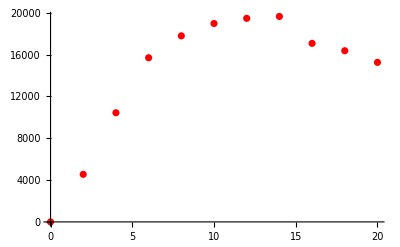

```mathematica
PlotMesInt=ListPlot[DistanceDataMes,PlotStyle->Red]
```

```mathematica
(*Field Strength*)
Fmunu=Table[D[Arat[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arat[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arat[{y[1],y[2],y[3],0}][[mu]][[b]]Arat[{y[1],y[2],y[3],0}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
B[y1_,y2_,y3_,t_]:=Table[1/2Sum[LeviCivitaTensor[3][[i]][[j]][[k]](Fmunu[[j]][[k]][[a]]/.{y[1]->y1,y[2]->y2,y[3]->y3,y[4]->t})PauliMatrix[a] ,{j,1,3},{k,1,3},{a,1,3}],{i,1,3}]
```

```mathematica
B[ypoint[[1]],ypoint[[2]],ypoint[[3]],1][[1]]/.{θ3->1.,θ1->0,θ2->0}
```

{{-0.0664156,0.0246322+0.0378125 ⅈ},{0.0246322-0.0378125 ⅈ,0.0664156}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y1_,y2_,y3_,t1_,t2_]:=Sum[Tr[WApproxLower[{y1,y2,y3,0},t1].B[y1,y2,y3,t1][[i]].WApproxUpper[{y1,y2,y3,0},t1].WdApproxUpper[{y1-r,y2,y3,0},t2].B[y1,y2,y3,t1][[i]].WdApproxLower[{y1-r,y2,y3,0},t2]],{i,1,3}]
```

```mathematica
AbsoluteTiming[ImesBB[ypoint[[1]],ypoint[[2]],ypoint[[3]],1,1]/.{θ3->1.,θ1->0,θ2->0}]
```

{1701.39,0.136186+0. ⅈ}

```mathematica
AngleDataMesBB=Table[{θ3,Sum[(L/n)^2*NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]ImesBB[y1,y2,y3,t1,t2],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2],{t1,1,n},{t2,1,n}]},{θ3,0,Pi,Pi/4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.92062+2.09352×10^-18 ⅈ and 0.0233804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.71502-2.1027×10^-18 ⅈ and 0.0214771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.00101-2.31235×10^-18 ⅈ and 0.0179915 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot[AngleDataMesBB]
```

```mathematica
(*SU(3) matrix for baryon*)
WapproxBar[y_]:=ArrayFlatten[{{Wapprox[y],0},{0,1}}]
```

```mathematica
Sum[LeviCivitaTensor[3][[b1]][[b2]][[b3]]LeviCivitaTensor[3][[c1]][[c2]][[c3]]w1[b1,c1]w2[b2,c2]KroneckerDelta[b3,c3],{b1,1,3},{b2,1,3},{b3,1,3},{c1,1,3},{c2,1,3},{c3,1,3}]
```

w1[2,2] w2[1,1]+w1[3,3] w2[1,1]-w1[2,1] w2[1,2]-w1[3,1] w2[1,3]-w1[1,2] w2[2,1]+w1[1,1] w2[2,2]+w1[3,3] w2[2,2]-w1[3,2] w2[2,3]-w1[1,3] w2[3,1]-w1[2,3] w2[3,2]+w1[1,1] w2[3,3]+w1[2,2] w2[3,3]

```mathematica
(*Baryon Integrand-Direct Triangle*)
Ibar[y_,rr_]:=(*1-1/6(WapproxBar[y][[2]][[2]]WapproxBar[y-{rr,0,0,0}][[1]][[1]]+
WapproxBar[y][[3]][[3]]WapproxBar[y-{rr,0,0,0}][[1]][[1]]-
WapproxBar[y][[2]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[2]]-
WapproxBar[y][[3]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[3]]-
WapproxBar[y][[1]][[2]]WapproxBar[y-{rr,0,0,0}][[2]][[1]]+
WapproxBar[y][[1]][[1]]WapproxBar[y-{rr,0,0,0}][[2]][[2]]+
WapproxBar[y][[3]][[3]]WapproxBar[y-{rr,0,0,0}][[2]][[2]]-
WapproxBar[y][[3]][[2]]WapproxBar[y-{rr,0,0,0}][[2]][[3]]-
WapproxBar[y][[3]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[3]]-
WapproxBar[y][[2]][[3]]WapproxBar[y-{rr,0,0,0}][[3]][[2]]+
WapproxBar[y][[1]][[1]]WapproxBar[y-{rr,0,0,0}][[3]][[3]]+
WapproxBar[y][[2]][[2]]WapproxBar[y-{rr,0,0,0}][[3]][[3]]
)*)1-1/6(LeviCivitaTensor[3].WapproxBar[y][[1]].WapproxBar[y-{rr,0,0,0}][[2]].WapproxBar[y-{0,rr,0,0}][[3]]+
LeviCivitaTensor[3].WapproxBar[y][[3]].WapproxBar[y-{rr,0,0,0}][[1]].WapproxBar[y-{0,rr,0,0}][[2]]+LeviCivitaTensor[3].WapproxBar[y][[2]].WapproxBar[y-{rr,0,0,0}][[3]].WapproxBar[y-{0,rr,0,0}][[1]]-
LeviCivitaTensor[3].WapproxBar[y][[1]].WapproxBar[y-{rr,0,0,0}][[3]].WapproxBar[y-{0,rr,0,0}][[2]]-
LeviCivitaTensor[3].WapproxBar[y][[2]].WapproxBar[y-{rr,0,0,0}][[1]].WapproxBar[y-{0,rr,0,0}][[3]]-LeviCivitaTensor[3].WapproxBar[y][[3]].WapproxBar[y-{rr,0,0,0}][[2]].WapproxBar[y-{0,rr,0,0}][[1]])
```

```mathematica
AbsoluteTiming[Ibar[{100,100,100,0},r]/.{θ3->1.,θ1->0,θ2->0}]
```

{26.6473,6.86381×10^-7+3.5293×10^-23 ⅈ}

```mathematica
AbsoluteTiming[Ibar2[ypoint]/.{θ3->1.,θ1->0,θ2->0}]
```

{280.352,1.-0.0825364 ⅈ}

```mathematica
AngleDataBar=Table[{θ3,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Ibar[{y1,y2,y3,0},r],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{θ3,0,Pi,Pi/20}]
```

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1] Sin[π/20]^2 Sin[θ2])/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand ((-1+√5)^2 Ibar[{y1,y2,y3,0},1] Sin[θ2])/(32 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1] Sin[(3 π)/20]^2 Sin[θ2])/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0,0.},{π/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/4,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(7 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(2 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(9 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/2,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(11 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(13 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(7 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/4,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(4 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(17 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(9 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(19 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π,0.}}

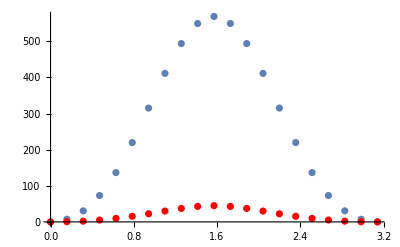

```mathematica
Show[ListPlot[AngleDataBar],ListPlot[AngleDataMes, PlotStyle->Red]]
```

```mathematica
DistanceDataBar=Table[{rr,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Sin[θ6]^2Sin[θ5]Ibar[{y1,y2,y3,0},rr],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{θ4,0,2Pi},{θ5,0,Pi},{θ6,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{rr,0,5,0.5}]
```

$Aborted

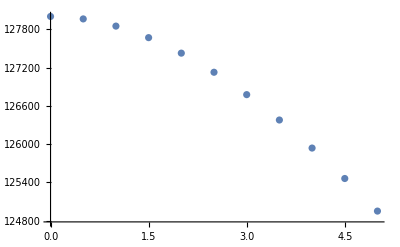

```mathematica
ListPlot[DistanceDataBar]
```

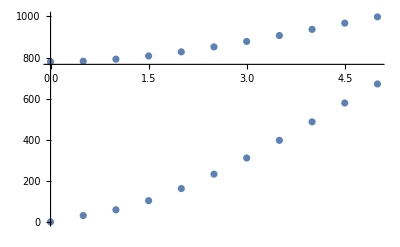

```mathematica
Show[ListPlot[{{0.,778.9835213308644},{0.5,782.3267046267691},{1.,792.152492607173},{1.5,807.7028960522447},{2.,827.7081944981895},{2.5,851.8575212904334},{3.,878.4555047811792},{3.5,907.1199034362559},{4.,937.2130977795467},{4.5,967.6137088101215},{5.,998.061197351786}}], ListPlot[{{0.,0.002512441216923788},{0.5,30.91367243239993},{1.,58.91338735249828},{1.5,103.40412743171798},{2.,162.2505756110101},{2.5,232.31559924567807},{3.,311.0906448660886},{3.5,396.9399695224351},{4.,486.9764667481333},{4.5,578.8795437770816},{5.,671.5149104549458}}],PlotStyle->Red,PlotRange->{0,1000}]
```

```mathematica
DistanceDataMes=
```

DistanceDataMes

$Aborted